# Signal & FT

Malcolm Levitt & Christian Bengs 01-July-2023
This documentation applies to SpinDynamica v3.10

Parts 1-6 of this documentation should be read first.

more advanced topics use this colour

## Setup

The code in this notebook requires the installation and initialization of SpinDynamica, as described in part 1 of the documentation

```mathematica
Needs["SpinDynamica`"];
SetSpinSystem[2];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

## Signal

The output of Signal1D is a Signal object. This is not just a set of times and signal amplitudes, but a software object which contains the information needed for the signal processing and plotting.

The Signal object may either contain frequency-domain information, or time-domain information. The choice depends upon the algorithm used by Signal1D. If Signal1D is run with the option SignalCalculationMethod→”Diagonalization” or SignalCalculationMethod→”Compute”, the output of Signal1D is in the frequency domain. If Signal1D is run with SignalCalculationMethod→”Direct”, the output of Signal1D is in the time domain.

If Signal1D is run with the default option SignalCalculationMethod→Automatic, the algorithm is chosen by the software, with the results as described above.

In most cases the user does not need to know the type of format, since the syntax for the subsequent processing is identical. In some cases, however, more detailed knowledge is useful. This is given below.

### Signal as a frequency-domain object

In the following simulation, Signal1D is used to calculate the spectrum generated by a Hamiltonian for a strongly-coupled 2-spin-1/2 system. The option SignalCalculationMethod→”Diagonalization” is chosen automatically in this case, and the result is a Signal object, in the frequency-domain format.

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, 128}},H]
```

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

Signal[{0,210.×10^-3,1.66667×10^-3}, {Lorentzian,<<4>>}]

#### format of Signal (frequency domain)

The first argument of Signal is given by the sampling specifications {tmin, tmax, δt}, where tmin and tmax are the time-coordinates of the first and last data point, and δt is the sampling interval (“dwell time”)

```mathematica
First[sig]
```

{0,21/100,1/600}

The second argument of Signal, in the case of a frequency-domain format, is a set of specifications for the spectral peaks:

```mathematica
sig⟦2⟧
```

{Lorentzian,{{0.200971,801.477,21.9294},{0.299029,-801.477,21.9294},{0.200971,-1113.16,21.9294},{0.299029,489.792,21.9294}}}

The format is as follows:
	{LineShapeType,{ {a_1, ω_1, λ_1}, {a_2, ω_2, λ_2},..}}
where LineShapeType is a String (here equal to “Lorentzian”), and each spectral peak is specified as a list of the form {a_i, ω_i, λ_i}.

The amplitude a_i is, in general, a complex number; a real value generates an absorption-mode peak upon processing, while an imaginary value generates a dispersion-mode peak upon processing.

The centre frequency of the peak ω_i is specified in rad s^-1.

The width of the peak λ_i is also specified in rad s^-1. In the case of a Lorentzian peak, λ_i is the half-width at half-height, in rad s^-1.

#### expanding and plotting Signal in the time domain

Signal may be converted into a set of {time,amplitude} pairs in the time domain by applying Expand:

```mathematica
Expand[sig]
```

{{0,1.},{1/600,0.256176-0.068642 ⅈ},{1/300,-0.585115+0.337816 ⅈ},{1/200,-0.35804+0.35804 ⅈ},{1/150,0.0673781-0.116702 ⅈ},{1/120,0.0671595-0.250643 ⅈ},{1/100,0.-0.155597 ⅈ},{7/600,-0.054745-0.204311 ⅈ},{1/75,0.00221559+0.00383751 ⅈ},{3/200,0.343393+0.343393 ⅈ},{1/60,0.327359+0.189001 ⅈ},{11/600,-0.352623-0.0944852 ⅈ},{1/50,-0.613992},{13/600,0.0131875-0.00353359 ⅈ},{7/300,0.435678-0.251539 ⅈ},{1/40,0.163893-0.163893 ⅈ},{2/75,-0.0843931+0.146173 ⅈ},{17/600,-0.0444856+0.166022 ⅈ},{3/100,0.+0.0907186 ⅈ},{19/600,0.0269649+0.100634 ⅈ},{1/30,-0.0402656-0.069742 ⅈ},{7/200,-0.236235-0.236235 ⅈ},{11/300,-0.120295-0.0694523 ⅈ},{23/600,0.318377+0.0853089 ⅈ},{1/25,0.338015},{1/24,-0.122752+0.0328913 ⅈ},{13/300,-0.291623+0.168368 ⅈ},{9/200,-0.0523292+0.0523292 ⅈ},{7/150,0.075607-0.130955 ⅈ},{29/600,0.0266921-0.0996164 ⅈ},{1/20,0.-0.0466795 ⅈ},{31/600,-0.0103409-0.0385928 ⅈ},{4/75,0.0485239+0.0840458 ⅈ},{11/200,0.147256+0.147256 ⅈ},{17/300,0.0115533+0.00667029 ⅈ},{7/120,-0.244286-0.0654562 ⅈ},{3/50,-0.159684},{37/600,0.145252-0.0389201 ⅈ},{19/300,0.176885-0.102125 ⅈ},{13/200,-0.00391307+0.00391307 ⅈ},{1/15,-0.0577403+0.100009 ⅈ},{41/600,-0.0142734+0.0532692 ⅈ},{7/100,0.+0.0195867 ⅈ},{43/600,0.00148225+0.00553183 ⅈ},{11/150,-0.0428378-0.0741973 ⅈ},{3/40,-0.0825649-0.0825649 ⅈ},{23/300,0.0358502+0.0206981 ⅈ},{47/600,0.167548+0.0448944 ⅈ},{2/25,0.0554893},{49/600,-0.127307+0.0341119 ⅈ},{1/12,-0.0959095+0.0553734 ⅈ},{17/200,0.0265718-0.0265718 ⅈ},{13/150,0.0394549-0.068338 ⅈ},{53/600,0.0064248-0.0239777 ⅈ},{9/100,0.-0.00463553 ⅈ},{11/120,0.00248118+0.0092599 ⅈ},{7/75,0.0324203+0.0561536 ⅈ},{19/200,0.0401361+0.0401361 ⅈ},{29/300,-0.0488291-0.0281915 ⅈ},{59/600,-0.104134-0.0279026 ⅈ},{1/10,-0.00171855},{61/600,0.0959131-0.0256998 ⅈ},{31/300,0.0441989-0.0255182 ⅈ},{21/200,-0.0310021+0.0310021 ⅈ},{8/75,-0.0244326+0.0423185 ⅈ},{13/120,-0.00195242+0.00728653 ⅈ},{11/100,0.-0.00245487 ⅈ},{67/600,-0.0036634-0.013672 ⅈ},{17/150,-0.021993-0.0380929 ⅈ},{23/200,-0.0149431-0.0149431 ⅈ},{7/60,0.0450492+0.0260092 ⅈ},{71/600,0.0581822+0.0155899 ⅈ},{3/25,-0.0209708},{73/600,-0.0648253+0.0173699 ⅈ},{37/300,-0.0143814+0.00830308 ⅈ},{1/8,0.0270174-0.0270174 ⅈ},{19/150,0.0135913-0.0235408 ⅈ},{77/600,-0.000274896+0.00102593 ⅈ},{13/100,0.+0.00494271 ⅈ},{79/600,0.00346653+0.0129373 ⅈ},{2/15,0.0135216+0.02342 ⅈ},{27/200,0.00165501+0.00165501 ⅈ},{41/300,-0.0350089-0.0202124 ⅈ},{83/600,-0.0281316-0.00753783 ⅈ},{7/50,0.0264666},{17/120,0.0397088-0.0106399 ⅈ},{43/300,-0.000724725+0.00041842 ⅈ},{29/200,-0.0202814+0.0202814 ⅈ},{11/75,-0.00652697+0.011305 ⅈ},{89/600,0.00114969-0.0042907 ⅈ},{3/20,0.-0.00504845 ⅈ},{91/600,-0.00273303-0.0101998 ⅈ},{23/150,-0.00745614-0.0129144 ⅈ},{31/200,0.00418335+0.00418335 ⅈ},{47/300,0.0242519+0.0140018 ⅈ},{19/120,0.0103439+0.00277163 ⅈ},{4/25,-0.0237776},{97/600,-0.0217972+0.00584055 ⅈ},{49/300,0.00687197-0.00396753 ⅈ},{33/200,0.0136671-0.0136671 ⅈ},{1/6,0.00236164-0.00409048 ⅈ},{101/600,-0.00129745+0.00484217 ⅈ},{17/100,0.+0.00414346 ⅈ},{103/600,0.00191419+0.00714386 ⅈ},{13/75,0.00353164+0.00611698 ⅈ},{7/40,-0.00582549-0.00582549 ⅈ},{53/300,-0.0152187-0.00878654 ⅈ},{107/600,-0.0010006-0.000268109 ⅈ},{9/50,0.0181896},{109/600,0.0102495-0.00274635 ⅈ},{11/60,-0.00813721+0.00469802 ⅈ},{37/200,-0.00834685+0.00834685 ⅈ},{14/75,-0.000185121+0.000320639 ⅈ},{113/600,0.00111503-0.00416136 ⅈ},{19/100,0.-0.00298817 ⅈ},{23/120,-0.00121377-0.00452987 ⅈ},{29/150,-0.00123537-0.00213972 ⅈ},{39/200,0.00541352+0.00541352 ⅈ},{59/300,0.00860063+0.00496557 ⅈ},{119/600,-0.00307388-0.000823644 ⅈ},{1/5,-0.0124461},{121/600,-0.00351955+0.000943062 ⅈ},{61/300,0.00713392-0.00411877 ⅈ},{41/200,0.00456487-0.00456487 ⅈ},{31/150,-0.000755013+0.00130772 ⅈ},{5/24,-0.000829557+0.00309595 ⅈ},{21/100,0.+0.00194592 ⅈ}}

The real and imaginary parts of the time-domain signal may be plotted using ListPlot:

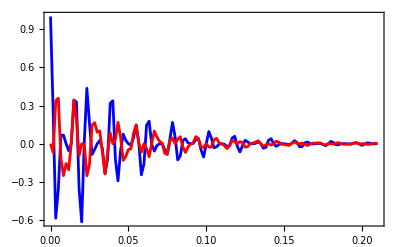

```mathematica
ListPlot[{Re[sig],Im[sig]},PlotStyle->{Blue,Red}]
```

Note that Expand is not needed here: SpinDynamica is programmed so that ListPlot “knows” to apply Expand without being told explicitly.

By default, the time-domain data is subjected to a default value of LineBroadening so as to improve the presentation of the spectrum after FourierTransformation (see below). In addition small manipulations of the peak frequencies are performed (see DigitalFrequencyResolution below). If you need an accurate representation of the “pure” time-domain data, both of these options may be disabled as follows:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

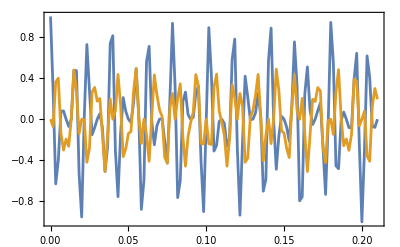

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, 128}},H,LineBroadening->None,DigitalFrequencyResolution->False];
ListPlot[{Re[sig],Im[sig]}]
```

#### plotting Signal in the frequency domain

Signal may be converted into the frequency-domain and plotted using the Fourier transform operation FT. The result is a set of {frequency, amplitude} pairs, where the frequency coordinates are here in Hz:

```mathematica
FT@sig
```

{{-37800/127,0.0000355902+0.000145256 ⅈ},{-37500/127,-0.0000581718+0.00182456 ⅈ},{-37200/127,0.0000811507+0.000318888 ⅈ},{-36900/127,-0.000104559+0.00199601 ⅈ},{-36600/127,0.00012843+0.000499704 ⅈ},{-36300/127,-0.0001528+0.00217008 ⅈ},{-36000/127,0.00017771+0.00068894 ⅈ},{-35700/127,-0.000203201+0.00234744 ⅈ},{-35400/127,0.00022932+0.000888034 ⅈ},{-35100/127,-0.000256117+0.0025288 ⅈ},{-34800/127,0.000283647+0.00109868 ⅈ},{-34500/127,-0.000311968+0.00271494 ⅈ},{-34200/127,0.000341146+0.0013229 ⅈ},{-33900/127,-0.000371253+0.00290673 ⅈ},{-33600/127,0.000402368+0.00156313 ⅈ},{-33300/127,-0.000434577+0.00310511 ⅈ},{-33000/127,0.000467977+0.00182233 ⅈ},{-32700/127,-0.000502675+0.00331116 ⅈ},{-32400/127,0.000538791+0.00210416 ⅈ},{-32100/127,-0.000576458+0.00352611 ⅈ},{-31800/127,0.000615829+0.00241323 ⅈ},{-31500/127,-0.000657071+0.00375135 ⅈ},{-31200/127,0.000700379+0.00275536 ⅈ},{-30900/127,-0.000745972+0.00398852 ⅈ},{-30600/127,0.000794101+0.00313812 ⅈ},{-30300/127,-0.000845054+0.00423956 ⅈ},{-30000/127,0.000899167+0.00357145 ⅈ},{-29700/127,-0.000956827+0.00450677 ⅈ},{-29400/127,0.00101849+0.00406878 ⅈ},{-29100/127,-0.00108469+0.00479297 ⅈ},{-28800/127,0.00115608+0.00464863 ⅈ},{-28500/127,-0.0012334+0.00510162 ⅈ},{-28200/127,0.00131758+0.00533734 ⅈ},{-27900/127,-0.00140976+0.00543714 ⅈ},{-27600/127,0.00151132+0.00617374 ⅈ},{-27300/127,-0.00162399+0.00580525 ⅈ},{-27000/127,0.00174998+0.00721747 ⅈ},{-26700/127,-0.0018921+0.00621371 ⅈ},{-26400/127,0.00205407+0.00856523 ⅈ},{-26100/127,-0.0022408+0.00667355 ⅈ},{-25800/127,0.00245903+0.0103848 ⅈ},{-25500/127,-0.00271822+0.00720166 ⅈ},{-25200/127,0.00303205+0.0129954 ⅈ},{-24900/127,-0.00342117+0.00782701 ⅈ},{-24600/127,0.00391818+0.0170875 ⅈ},{-24300/127,-0.00457788+0.00860857 ⅈ},{-24000/127,0.0055+0.0244866 ⅈ},{-23700/127,-0.00688734+0.00970741 ⅈ},{-23400/127,0.00922523+0.0421082 ⅈ},{-23100/127,-0.0140376+0.011915 ⅈ},{-22800/127,0.0298648+0.140552 ⅈ},{-22500/127,0.194943-0.0309692 ⅈ},{-22200/127,-0.0222544-0.108832 ⅈ},{-21900/127,0.0115811+0.00838875 ⅈ},{-21600/127,-0.00769776-0.0395536 ⅈ},{-21300/127,0.00567097+0.0108431 ⅈ},{-21000/127,-0.00441246-0.024222 ⅈ},{-20700/127,0.00354334+0.0128139 ⅈ},{-20400/127,-0.00289649-0.0174465 ⅈ},{-20100/127,0.00238614+0.0150312 ⅈ},{-19800/127,-0.00196299-0.013603 ⅈ},{-19500/127,0.00159573+0.0178658 ⅈ},{-19200/127,-0.00126235-0.0111086 ⅈ},{-18900/127,0.000945256+0.0218258 ⅈ},{-18600/127,-0.000628011-0.00934283 ⅈ},{-18300/127,0.00029211+0.0279258 ⅈ},{-18000/127,0.0000875149-0.00800947 ⅈ},{-17700/127,-0.000551134+0.0387539 ⅈ},{-17400/127,0.00117477-0.00693876 ⅈ},{-17100/127,-0.00213062+0.0636914 ⅈ},{-16800/127,0.00392486-0.00596945 ⅈ},{-16500/127,-0.00901262+0.184562 ⅈ},{-16200/127,0.297302+0.0110283 ⅈ},{-15900/127,0.0119888-0.195382 ⅈ},{-15600/127,-0.006356-0.00528703 ⅈ},{-15300/127,0.00448523-0.0625673 ⅈ},{-15000/127,-0.00353232-0.00463061 ⅈ},{-14700/127,0.00294431-0.0366918 ⅈ},{-14400/127,-0.00253884-0.00413528 ⅈ},{-14100/127,0.00223813-0.0256288 ⅈ},{-13800/127,-0.00200335-0.00371185 ⅈ},{-13500/127,0.0018129-0.0194649 ⅈ},{-13200/127,-0.00165379-0.00333557 ⅈ},{-12900/127,0.00151772-0.0155193 ⅈ},{-12600/127,-0.00139911-0.00299401 ⅈ},{-12300/127,0.00129409-0.0127651 ⅈ},{-12000/127,-0.00119985-0.0026792 ⅈ},{-11700/127,0.00111432-0.0107244 ⅈ},{-11400/127,-0.00103593-0.00238542 ⅈ},{-11100/127,0.00096346-0.0091444 ⅈ},{-10800/127,-0.000895953-0.00210828 ⅈ},{-10500/127,0.000832636-0.00787896 ⅈ},{-10200/127,-0.000772884-0.00184426 ⅈ},{-9900/127,0.000716178-0.00683754 ⅈ},{-9600/127,-0.000662088-0.00159045 ⅈ},{-9300/127,0.000610248-0.00596107 ⅈ},{-9000/127,-0.000560347-0.00134438 ⅈ},{-8700/127,0.000512114-0.00520934 ⅈ},{-8400/127,-0.000465316-0.00110386 ⅈ},{-8100/127,0.000419744-0.00455399 ⅈ},{-7800/127,-0.000375214-0.000866948 ⅈ},{-7500/127,0.00033156-0.00397439 ⅈ},{-7200/127,-0.000288632-0.000631821 ⅈ},{-6900/127,0.00024629-0.00345519 ⅈ},{-6600/127,-0.000204407-0.000396753 ⅈ},{-6300/127,0.000162862-0.00298465 ⅈ},{-6000/127,-0.000121542-0.000160047 ⅈ},{-5700/127,0.0000803372-0.00255363 ⅈ},{-5400/127,-0.0000391426+0.0000800074 ⅈ},{-5100/127,-2.14452×10^-6-0.00215486 ⅈ},{-4800/127,0.0000436258+0.000325186 ⅈ},{-4500/127,-0.0000854026-0.00178246 ⅈ},{-4200/127,0.000127577+0.000577379 ⅈ},{-3900/127,-0.000170252-0.00143157 ⅈ},{-3600/127,0.000213535+0.000838649 ⅈ},{-3300/127,-0.000257536-0.00109807 ⅈ},{-3000/127,0.00030237+0.0011113 ⅈ},{-2700/127,-0.000348157-0.000778458 ⅈ},{-2400/127,0.000395027+0.00139795 ⅈ},{-2100/127,-0.000443115-0.000469606 ⅈ},{-1800/127,0.000492569+0.00170164 ⅈ},{-1500/127,-0.000543548-0.000168703 ⅈ},{-1200/127,0.000596224+0.00202598 ⅈ},{-900/127,-0.000650786+0.000126874 ⅈ},{-600/127,0.000707442+0.0023753 ⅈ},{-300/127,-0.000766421+0.000419648 ⅈ},{0,0.000827978+0.0027549 ⅈ},{300/127,-0.000892397+0.000712132 ⅈ},{600/127,0.000959997+0.00317135 ⅈ},{900/127,-0.00103114+0.00100693 ⅈ},{1200/127,0.00110623+0.00363301 ⅈ},{1500/127,-0.00118573+0.00130682 ⅈ},{1800/127,0.00127018+0.00415063 ⅈ},{2100/127,-0.00136019+0.00161495 ⅈ},{2400/127,0.00145647+0.00473837 ⅈ},{2700/127,-0.00155984+0.00193494 ⅈ},{3000/127,0.00167129+0.00541527 ⅈ},{3300/127,-0.00179196+0.00227121 ⅈ},{3600/127,0.00192323+0.00620765 ⅈ},{3900/127,-0.00206674+0.00262932 ⅈ},{4200/127,0.0022245+0.00715295 ⅈ},{4500/127,-0.00239894+0.00301662 ⅈ},{4800/127,0.00259311+0.00830638 ⅈ},{5100/127,-0.0028108+0.00344332 ⅈ},{5400/127,0.00305685+0.00975291 ⅈ},{5700/127,-0.00333747+0.00392436 ⅈ},{6000/127,0.00366086+0.0116306 ⅈ},{6300/127,-0.00403797+0.00448324 ⅈ},{6600/127,0.00448383+0.0141796 ⅈ},{6900/127,-0.0050196+0.00516023 ⅈ},{7200/127,0.00567608+0.0178585 ⅈ},{7500/127,-0.00649988+0.00603309 ⅈ},{7800/127,0.00756506+0.0236653 ⅈ},{8100/127,-0.00899678+0.00728004 ⅈ},{8400/127,0.0110246+0.0342618 ⅈ},{8700/127,-0.01412+0.00944038 ⅈ},{9000/127,0.0194284+0.0599209 ⅈ},{9300/127,-0.0306439+0.0154104 ⅈ},{9600/127,0.0699788+0.213904 ⅈ},{9900/127,0.28011-0.086037 ⅈ},{10200/127,-0.047722-0.14432 ⅈ},{10500/127,0.0264091-0.00196491 ⅈ},{10800/127,-0.0184167-0.0549756 ⅈ},{11100/127,0.0142366+0.00292406 ⅈ},{11400/127,-0.0116723-0.0342851 ⅈ},{11700/127,0.0099441+0.00543883 ⅈ},{12000/127,-0.00870601-0.0250526 ⅈ},{12300/127,0.0077813+0.00756818 ⅈ},{12600/127,-0.00707084-0.0198064 ⅈ},{12900/127,0.00651535+0.00988998 ⅈ},{13200/127,-0.00607808-0.0164102 ⅈ},{13500/127,0.00573627+0.0128659 ⅈ},{13800/127,-0.00547698-0.0140209 ⅈ},{14100/127,0.00529559+0.0172473 ⅈ},{14400/127,-0.00519671-0.0122364 ⅈ},{14700/127,0.00519891+0.0248667 ⅈ},{15000/127,-0.00534865-0.0108334 ⅈ},{15300/127,0.00576383+0.0424039 ⅈ},{15600/127,-0.00681231-0.00963626 ⅈ},{15900/127,0.0104025+0.131785 ⅈ},{16200/127,0.19765-0.020094 ⅈ},{16500/127,-0.00407352-0.123468 ⅈ},{16800/127,0.000824494-0.00837729 ⅈ},{17100/127,0.000215226-0.042153 ⅈ},{17400/127,-0.000693746-0.00763775 ⅈ},{17700/127,0.000949254-0.0253278 ⅈ},{18000/127,-0.00109533-0.00704813 ⅈ},{18300/127,0.00118065-0.0180006 ⅈ},{18600/127,-0.0012294-0.00654306 ⅈ},{18900/127,0.00125491-0.0138682 ⅈ},{19200/127,-0.00126502-0.00609963 ⅈ},{19500/127,0.00126465-0.0111962 ⅈ},{19800/127,-0.00125701-0.00570454 ⅈ},{20100/127,0.00124423-0.00931401 ⅈ},{20400/127,-0.00122781-0.0053486 ⅈ},{20700/127,0.0012088-0.00790745 ⅈ},{21000/127,-0.00118795-0.00502496 ⅈ},{21300/127,0.00116582-0.00680974 ⅈ},{21600/127,-0.00114279-0.00472835 ⅈ},{21900/127,0.00111918-0.00592398 ⅈ},{22200/127,-0.00109522-0.00445456 ⅈ},{22500/127,0.00107106-0.00519005 ⅈ},{22800/127,-0.00104683-0.00420022 ⅈ},{23100/127,0.00102264-0.00456857 ⅈ},{23400/127,-0.000998547-0.00396253 ⅈ},{23700/127,0.000974605-0.00403271 ⅈ},{24000/127,-0.000950853-0.00373918 ⅈ},{24300/127,0.000927318-0.0035635 ⅈ},{24600/127,-0.000904018-0.00352823 ⅈ},{24900/127,0.000880963-0.00314716 ⅈ},{25200/127,-0.000858161-0.00332802 ⅈ},{25500/127,0.000835612-0.00277342 ⅈ},{25800/127,-0.000813316-0.00313715 ⅈ},{26100/127,0.000791269-0.00243445 ⅈ},{26400/127,-0.000769465-0.00295438 ⅈ},{26700/127,0.000747896-0.00212419 ⅈ},{27000/127,-0.000726555-0.00277864 ⅈ},{27300/127,0.00070543-0.00183785 ⅈ},{27600/127,-0.000684514-0.00260898 ⅈ},{27900/127,0.000663793-0.00157159 ⅈ},{28200/127,-0.000643258-0.00244455 ⅈ},{28500/127,0.000622897-0.0013223 ⅈ},{28800/127,-0.000602698-0.0022846 ⅈ},{29100/127,0.000582649-0.00108741 ⅈ},{29400/127,-0.000562738-0.00212843 ⅈ},{29700/127,0.000542953-0.000864793 ⅈ},{30000/127,-0.000523282-0.0019754 ⅈ},{30300/127,0.000503712-0.00065264 ⅈ},{30600/127,-0.000484232-0.00182492 ⅈ},{30900/127,0.000464827-0.000449421 ⅈ},{31200/127,-0.000445487-0.00167643 ⅈ},{31500/127,0.000426199-0.000253813 ⅈ},{31800/127,-0.000406949-0.00152938 ⅈ},{32100/127,0.000387725-0.0000646656 ⅈ},{32400/127,-0.000368515-0.00138326 ⅈ},{32700/127,0.000349304+0.000119038 ⅈ},{33000/127,-0.00033008-0.00123756 ⅈ},{33300/127,0.00031083+0.000298204 ⅈ},{33600/127,-0.000291539-0.00109176 ⅈ},{33900/127,0.000272193+0.000473651 ⅈ},{34200/127,-0.000252778-0.000945359 ⅈ},{34500/127,0.00023328+0.000646126 ⅈ},{34800/127,-0.000213683-0.000797812 ⅈ},{35100/127,0.000193971+0.000816323 ⅈ},{35400/127,-0.000174128-0.000648571 ⅈ},{35700/127,0.000154138+0.000984894 ⅈ},{36000/127,-0.000133983-0.000497052 ⅈ},{36300/127,0.000113644+0.00115246 ⅈ},{36600/127,-0.0000931027-0.000342627 ⅈ},{36900/127,0.0000723391+0.00131962 ⅈ},{37200/127,-0.0000513321-0.000184614 ⅈ},{37500/127,0.0000300597+0.00148696 ⅈ},{37800/127,-8.49859×10^-6-0.0000222648 ⅈ},{300,-0.000013376+0.00165508 ⅈ}}

The real part of the result may be plotted using ListPlot:

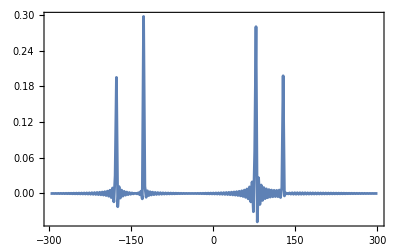

```mathematica
ListPlot[Re@FT@sig]
```

An expanded section may be plotted by using the PlotRange option of ListPlot:

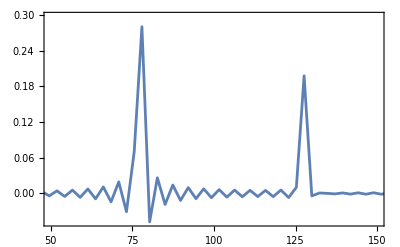

```mathematica
ListPlot[Re@FT@sig,PlotRange->{{50,150},All}]
```

The calculation above used only 128 data points. A more attractive result is obtained using a larger number of data points:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 860.59×10^-3 rad s^-1.

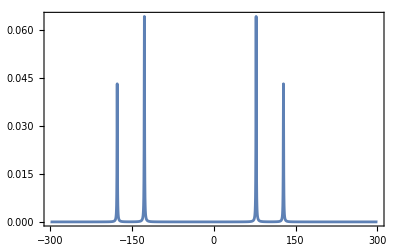

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot@Re@FT@Signal1D[{{2π 600, "1k"}},H]
```

#### DigitalFrequencyResolution

When Signal is generated in the frequency domain (by using Signal1D with SignalCalculationMethod→”Diagonalization” or “COMPUTE”), the peak frequencies ω_i are by default automatically “snapped” to the nearest digitization point in the frequency spectrum. This may be seen by plotting the data points on the spectrum:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

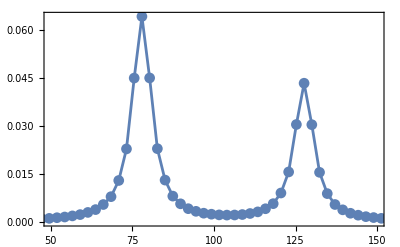

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[{{2π 600, 128}},H],
PlotRange->{{50,150},All},PlotMarkers->Automatic
]
```

The peaks are shifted slightly so that there is a data point at each peak maximum. This gives an attractive spectral representation, with good representation of the peak heights. However the small artificial shifts in the peak frequencies may be undesirable in some cases.

Peak “snapping” allows much faster processing of data with a large number of peaks in the spectrum.

The “snapping” of the peaks to the nearest data point in the frequency domain may be suppressed by running Signal1D with the option DigitalFrequencyResolution→False

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

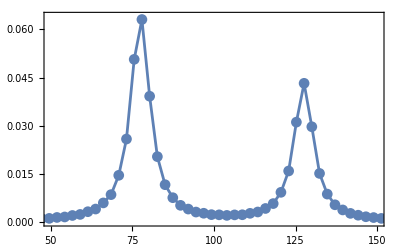

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[{{2π 600, 128}},H,DigitalFrequencyResolution->False],
PlotRange->{{50,150},All},PlotMarkers->Automatic
]
```

It is also possible to use a large value for ZeroFill (see below) to improve the digitization of the peak frequencies:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

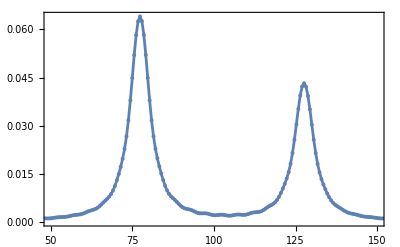

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[{{2π 600, 128}},H,ZeroFill->8],
PlotRange->{{50,150},All},PlotMarkers->{Automatic,Tiny}
]
```

In summary, the default options ZeroFill→Automatic and DigitalFrequencyResolution→Automatic give a good compromise between accuracy and computation speed. If higher accuracy is needed, ZeroFill may be set to a high value, and/or DigitalFrequencyResolution may be set to False.

#### ZeroFill

Zero-filling is a data processing procedure in which zeroes are appended to the data before Fourier transformation. This improves the digital frequency resolution of the resulting spectrum, at the expense of a modest increase in processing time. In SpinDynamica, zero-filling is controlled with the option ZeroFill.

If the time-domain data contains n complex points, the option ZeroFill→z appends (n-1)×z zeroes to the data before FT. Hence ZeroFill→1 does nothing and ZeroFill→4 multiplies the length of the data by 4.

By default, Signal1D generates a Signal with the option ZeroFill→Automatic. This is equivalent to ZeroFill→2, appending the same number of zeroes as the length of the data, before Fourier transformation.

Zero-filling may be suppressed by specifying ZeroFill→False

In the following simulation, zero-filling and DigitalFrequencyResolution are both suppressed. The resulting spectrum is not attractive:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

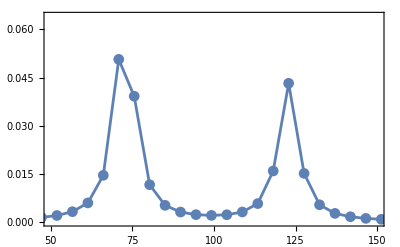

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[{{2π 600, 128}},H,ZeroFill->False,DigitalFrequencyResolution->False],
PlotRange->{{50,150},All},PlotMarkers->Automatic
]
```

Default zero-filling gives a better-looking result:

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[{{2π 600, 128}},H,DigitalFrequencyResolution->False],
PlotRange->{{50,150},All},PlotMarkers->Automatic
]
```

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

-Graphics-

A more accurate spectral representation is generated by adding zeroes to increase the data length by a factor of 8 before Fourier transformation:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

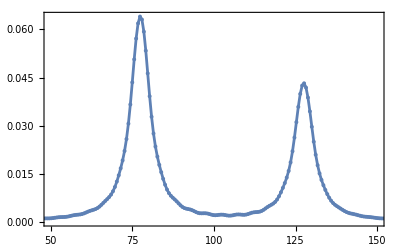

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[{{2π 600, 128}},H,DigitalFrequencyResolution->False,ZeroFill->8],
PlotRange->{{50,150},All},PlotMarkers->{Automatic,Tiny}
]
```

#### LineBroadening

Artifical Lorentzian broadening may be added to the signal by using the option LineBroadening within Signal1D. The value of LineBroadening is the half-width and half-height of the Lorentzian broadening function, in rad s^-1.

The default option LineBroadening→Automatic applies an exponential decay function to the time-domain data which starts at 1.0 and reaches the value 0.01 at the end of the acquired data points. The resulting value of LineBroadening is reported when Signal1D is run. In the case below a line-broadening with half-width at half-height of 6.93 Hz is applied:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

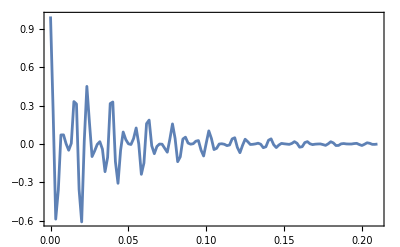

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@Signal1D[{{2π 600, 128}},H]
]
```

The message may be suppressed, if desired, by executing Off[Signal1D::autolb].

Line-broadening may be suppressed by the option LineBroadening→None:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

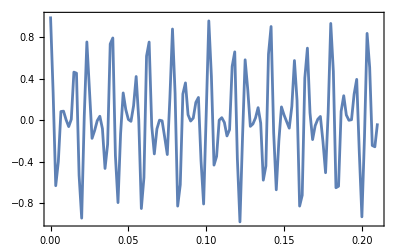

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
ListPlot[
Re@Signal1D[{{2π 600, 128}},H,LineBroadening->None]
]
```

#### post-calculation processing options

The options ZeroFill and LineBroadening may applied at the Fourier transformation stage, after the Signal1D calculation.

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, 128}},H, LineBroadening->None]
```

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal[{0,210.×10^-3,1.66667×10^-3}, {Lorentzian,<<4>>}]

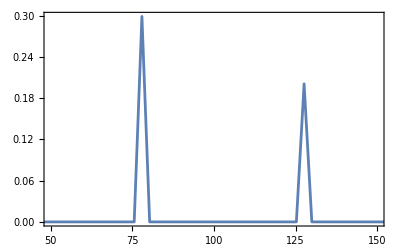

```mathematica
ListPlot[
Re@FT[sig],
PlotRange->{{50,150},All}
]
```

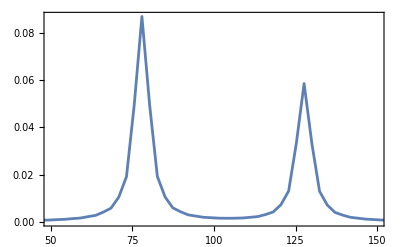

```mathematica
ListPlot[
Re@FT[sig,LineBroadening->2π 5],
PlotRange->{{50,150},All}
]
```

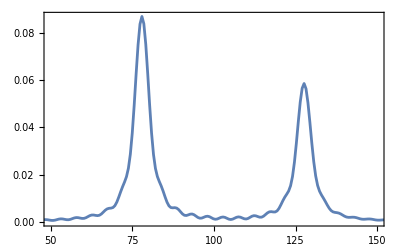

```mathematica
ListPlot[
Re@FT[sig,LineBroadening->2π 5,ZeroFill->8],
PlotRange->{{50,150},All}
]
```

The option DigitalFrequencyResolution, on the other hand, must be executed at the time of Signal1D.

### Signal as a time-domain object

In the following simulation, Signal1D is used with the explicit option SignalCalculationMethod→”Direct”. In this case, the result is a Signal object, in the time-domain format.

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, 128}},H,SignalCalculationMethod->"Direct"]
```

Signal1D::reportscm: Using SignalCalculationMethod → Direct

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

Signal[{0,210.×10^-3,1.66667×10^-3}, <<127>>]

In some cases, Signal1D will choose SignalCalculationMethod→”Direct” automatically (see Part 2 of the documentation).

#### format of Signal (time domain)

The first argument of Signal is given by the sampling specifications {tmin, tmax, δt}, where tmin and tmax are the time-coordinates of the first and last data point, and δt is the sampling interval (“dwell time”)

```mathematica
First[sig]
```

{0,21/100,1/600}

The second argument of Signal, in the case of a time-domain format, is the set of complex signal amplitudes:

```mathematica
sig⟦2⟧
```

{1.,0.256176-0.068642 ⅈ,-0.585115+0.337816 ⅈ,-0.35804+0.35804 ⅈ,0.0673781-0.116702 ⅈ,0.0671595-0.250643 ⅈ,0.-0.155597 ⅈ,-0.054745-0.204311 ⅈ,0.00221559+0.00383751 ⅈ,0.343393+0.343393 ⅈ,0.327359+0.189001 ⅈ,-0.352623-0.0944852 ⅈ,-0.613992,0.0131875-0.00353359 ⅈ,0.435678-0.251539 ⅈ,0.163893-0.163893 ⅈ,-0.0843931+0.146173 ⅈ,-0.0444856+0.166022 ⅈ,0.+0.0907186 ⅈ,0.0269649+0.100634 ⅈ,-0.0402656-0.069742 ⅈ,-0.236235-0.236235 ⅈ,-0.120295-0.0694523 ⅈ,0.318377+0.0853089 ⅈ,0.338015,-0.122752+0.0328913 ⅈ,-0.291623+0.168368 ⅈ,-0.0523292+0.0523292 ⅈ,0.075607-0.130955 ⅈ,0.0266921-0.0996164 ⅈ,0.-0.0466795 ⅈ,-0.0103409-0.0385928 ⅈ,0.0485239+0.0840458 ⅈ,0.147256+0.147256 ⅈ,0.0115533+0.00667029 ⅈ,-0.244286-0.0654562 ⅈ,-0.159684,0.145252-0.0389201 ⅈ,0.176885-0.102125 ⅈ,-0.00391307+0.00391307 ⅈ,-0.0577403+0.100009 ⅈ,-0.0142734+0.0532692 ⅈ,0.+0.0195867 ⅈ,0.00148225+0.00553183 ⅈ,-0.0428378-0.0741973 ⅈ,-0.0825649-0.0825649 ⅈ,0.0358502+0.0206981 ⅈ,0.167548+0.0448944 ⅈ,0.0554893,-0.127307+0.0341119 ⅈ,-0.0959095+0.0553734 ⅈ,0.0265718-0.0265718 ⅈ,0.0394549-0.068338 ⅈ,0.0064248-0.0239777 ⅈ,0.-0.00463553 ⅈ,0.00248118+0.0092599 ⅈ,0.0324203+0.0561536 ⅈ,0.0401361+0.0401361 ⅈ,-0.0488291-0.0281915 ⅈ,-0.104134-0.0279026 ⅈ,-0.00171855,0.0959131-0.0256998 ⅈ,0.0441989-0.0255182 ⅈ,-0.0310021+0.0310021 ⅈ,-0.0244326+0.0423185 ⅈ,-0.00195242+0.00728653 ⅈ,0.-0.00245487 ⅈ,-0.0036634-0.013672 ⅈ,-0.021993-0.0380929 ⅈ,-0.0149431-0.0149431 ⅈ,0.0450492+0.0260092 ⅈ,0.0581822+0.0155899 ⅈ,-0.0209708,-0.0648253+0.0173699 ⅈ,-0.0143814+0.00830308 ⅈ,0.0270174-0.0270174 ⅈ,0.0135913-0.0235408 ⅈ,-0.000274896+0.00102593 ⅈ,0.+0.00494271 ⅈ,0.00346653+0.0129373 ⅈ,0.0135216+0.02342 ⅈ,0.00165501+0.00165501 ⅈ,-0.0350089-0.0202124 ⅈ,-0.0281316-0.00753783 ⅈ,0.0264666,0.0397088-0.0106399 ⅈ,-0.000724725+0.00041842 ⅈ,-0.0202814+0.0202814 ⅈ,-0.00652697+0.011305 ⅈ,0.00114969-0.0042907 ⅈ,0.-0.00504845 ⅈ,-0.00273303-0.0101998 ⅈ,-0.00745614-0.0129144 ⅈ,0.00418335+0.00418335 ⅈ,0.0242519+0.0140018 ⅈ,0.0103439+0.00277163 ⅈ,-0.0237776,-0.0217972+0.00584055 ⅈ,0.00687197-0.00396753 ⅈ,0.0136671-0.0136671 ⅈ,0.00236164-0.00409048 ⅈ,-0.00129745+0.00484217 ⅈ,0.+0.00414346 ⅈ,0.00191419+0.00714386 ⅈ,0.00353164+0.00611698 ⅈ,-0.00582549-0.00582549 ⅈ,-0.0152187-0.00878654 ⅈ,-0.0010006-0.000268109 ⅈ,0.0181896,0.0102495-0.00274635 ⅈ,-0.00813721+0.00469802 ⅈ,-0.00834685+0.00834685 ⅈ,-0.000185121+0.000320639 ⅈ,0.00111503-0.00416136 ⅈ,0.-0.00298817 ⅈ,-0.00121377-0.00452987 ⅈ,-0.00123537-0.00213972 ⅈ,0.00541352+0.00541352 ⅈ,0.00860063+0.00496557 ⅈ,-0.00307388-0.000823644 ⅈ,-0.0124461,-0.00351955+0.000943062 ⅈ,0.00713392-0.00411877 ⅈ,0.00456487-0.00456487 ⅈ,-0.000755013+0.00130772 ⅈ,-0.000829557+0.00309595 ⅈ,0.+0.00194592 ⅈ}

#### expanding and plotting Signal in the time domain

As in the frequency-domain case, Signal may be converted into a set of {time,amplitude} pairs in the time domain by applying Expand:

```mathematica
Expand[sig]
```

{{0,1.},{1/600,0.256176-0.068642 ⅈ},{1/300,-0.585115+0.337816 ⅈ},{1/200,-0.35804+0.35804 ⅈ},{1/150,0.0673781-0.116702 ⅈ},{1/120,0.0671595-0.250643 ⅈ},{1/100,0.-0.155597 ⅈ},{7/600,-0.054745-0.204311 ⅈ},{1/75,0.00221559+0.00383751 ⅈ},{3/200,0.343393+0.343393 ⅈ},{1/60,0.327359+0.189001 ⅈ},{11/600,-0.352623-0.0944852 ⅈ},{1/50,-0.613992},{13/600,0.0131875-0.00353359 ⅈ},{7/300,0.435678-0.251539 ⅈ},{1/40,0.163893-0.163893 ⅈ},{2/75,-0.0843931+0.146173 ⅈ},{17/600,-0.0444856+0.166022 ⅈ},{3/100,0.+0.0907186 ⅈ},{19/600,0.0269649+0.100634 ⅈ},{1/30,-0.0402656-0.069742 ⅈ},{7/200,-0.236235-0.236235 ⅈ},{11/300,-0.120295-0.0694523 ⅈ},{23/600,0.318377+0.0853089 ⅈ},{1/25,0.338015},{1/24,-0.122752+0.0328913 ⅈ},{13/300,-0.291623+0.168368 ⅈ},{9/200,-0.0523292+0.0523292 ⅈ},{7/150,0.075607-0.130955 ⅈ},{29/600,0.0266921-0.0996164 ⅈ},{1/20,0.-0.0466795 ⅈ},{31/600,-0.0103409-0.0385928 ⅈ},{4/75,0.0485239+0.0840458 ⅈ},{11/200,0.147256+0.147256 ⅈ},{17/300,0.0115533+0.00667029 ⅈ},{7/120,-0.244286-0.0654562 ⅈ},{3/50,-0.159684},{37/600,0.145252-0.0389201 ⅈ},{19/300,0.176885-0.102125 ⅈ},{13/200,-0.00391307+0.00391307 ⅈ},{1/15,-0.0577403+0.100009 ⅈ},{41/600,-0.0142734+0.0532692 ⅈ},{7/100,0.+0.0195867 ⅈ},{43/600,0.00148225+0.00553183 ⅈ},{11/150,-0.0428378-0.0741973 ⅈ},{3/40,-0.0825649-0.0825649 ⅈ},{23/300,0.0358502+0.0206981 ⅈ},{47/600,0.167548+0.0448944 ⅈ},{2/25,0.0554893},{49/600,-0.127307+0.0341119 ⅈ},{1/12,-0.0959095+0.0553734 ⅈ},{17/200,0.0265718-0.0265718 ⅈ},{13/150,0.0394549-0.068338 ⅈ},{53/600,0.0064248-0.0239777 ⅈ},{9/100,0.-0.00463553 ⅈ},{11/120,0.00248118+0.0092599 ⅈ},{7/75,0.0324203+0.0561536 ⅈ},{19/200,0.0401361+0.0401361 ⅈ},{29/300,-0.0488291-0.0281915 ⅈ},{59/600,-0.104134-0.0279026 ⅈ},{1/10,-0.00171855},{61/600,0.0959131-0.0256998 ⅈ},{31/300,0.0441989-0.0255182 ⅈ},{21/200,-0.0310021+0.0310021 ⅈ},{8/75,-0.0244326+0.0423185 ⅈ},{13/120,-0.00195242+0.00728653 ⅈ},{11/100,0.-0.00245487 ⅈ},{67/600,-0.0036634-0.013672 ⅈ},{17/150,-0.021993-0.0380929 ⅈ},{23/200,-0.0149431-0.0149431 ⅈ},{7/60,0.0450492+0.0260092 ⅈ},{71/600,0.0581822+0.0155899 ⅈ},{3/25,-0.0209708},{73/600,-0.0648253+0.0173699 ⅈ},{37/300,-0.0143814+0.00830308 ⅈ},{1/8,0.0270174-0.0270174 ⅈ},{19/150,0.0135913-0.0235408 ⅈ},{77/600,-0.000274896+0.00102593 ⅈ},{13/100,0.+0.00494271 ⅈ},{79/600,0.00346653+0.0129373 ⅈ},{2/15,0.0135216+0.02342 ⅈ},{27/200,0.00165501+0.00165501 ⅈ},{41/300,-0.0350089-0.0202124 ⅈ},{83/600,-0.0281316-0.00753783 ⅈ},{7/50,0.0264666},{17/120,0.0397088-0.0106399 ⅈ},{43/300,-0.000724725+0.00041842 ⅈ},{29/200,-0.0202814+0.0202814 ⅈ},{11/75,-0.00652697+0.011305 ⅈ},{89/600,0.00114969-0.0042907 ⅈ},{3/20,0.-0.00504845 ⅈ},{91/600,-0.00273303-0.0101998 ⅈ},{23/150,-0.00745614-0.0129144 ⅈ},{31/200,0.00418335+0.00418335 ⅈ},{47/300,0.0242519+0.0140018 ⅈ},{19/120,0.0103439+0.00277163 ⅈ},{4/25,-0.0237776},{97/600,-0.0217972+0.00584055 ⅈ},{49/300,0.00687197-0.00396753 ⅈ},{33/200,0.0136671-0.0136671 ⅈ},{1/6,0.00236164-0.00409048 ⅈ},{101/600,-0.00129745+0.00484217 ⅈ},{17/100,0.+0.00414346 ⅈ},{103/600,0.00191419+0.00714386 ⅈ},{13/75,0.00353164+0.00611698 ⅈ},{7/40,-0.00582549-0.00582549 ⅈ},{53/300,-0.0152187-0.00878654 ⅈ},{107/600,-0.0010006-0.000268109 ⅈ},{9/50,0.0181896},{109/600,0.0102495-0.00274635 ⅈ},{11/60,-0.00813721+0.00469802 ⅈ},{37/200,-0.00834685+0.00834685 ⅈ},{14/75,-0.000185121+0.000320639 ⅈ},{113/600,0.00111503-0.00416136 ⅈ},{19/100,0.-0.00298817 ⅈ},{23/120,-0.00121377-0.00452987 ⅈ},{29/150,-0.00123537-0.00213972 ⅈ},{39/200,0.00541352+0.00541352 ⅈ},{59/300,0.00860063+0.00496557 ⅈ},{119/600,-0.00307388-0.000823644 ⅈ},{1/5,-0.0124461},{121/600,-0.00351955+0.000943062 ⅈ},{61/300,0.00713392-0.00411877 ⅈ},{41/200,0.00456487-0.00456487 ⅈ},{31/150,-0.000755013+0.00130772 ⅈ},{5/24,-0.000829557+0.00309595 ⅈ},{21/100,0.+0.00194592 ⅈ}}

As before, the real and imaginary parts of the time-domain signal may be plotted using ListPlot:

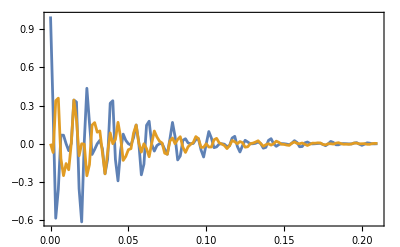

```mathematica
ListPlot[{Re[sig],Im[sig]}]
```

By default, the time-domain data is subjected to a default value of LineBroadening so as to improve the presentation of the spectrum after FourierTransformation. As in the frequency-domain case, LineBroadening→None may be used to suppress this.

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, 128}},H,LineBroadening->None,SignalCalculationMethod->"Direct"];
ListPlot[{Re[sig],Im[sig]}]
```

Signal1D::reportscm: Using SignalCalculationMethod → Direct

-Graphics-

The option DigitalFrequencyResolution does not apply for a time-domain Signal object.

#### plotting Signal in the frequency domain

A time-domain Signal may be converted into the frequency domain using the Fourier transform operation FT. The result is a set of {frequency, amplitude} pairs, where the frequency coordinates are here in Hz:

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, 128}},H,SignalCalculationMethod->"Direct"];FT@sig
```

Signal1D::reportscm: Using SignalCalculationMethod → Direct

Signal1D::autolb: Using LineBroadening → 2π × 6.98034 rad s^-1.

{{-37800/127,0.000125827+0.000933363 ⅈ},{-37500/127,0.000126423+0.00103474 ⅈ},{-37200/127,0.000129452+0.00110515 ⅈ},{-36900/127,0.00012945+0.00120875 ⅈ},{-36600/127,0.000133753+0.00128167 ⅈ},{-36300/127,0.000133151+0.00138791 ⅈ},{-36000/127,0.000138813+0.00146386 ⅈ},{-35700/127,0.000137614+0.0015732 ⅈ},{-35400/127,0.000144737+0.00165278 ⅈ},{-35100/127,0.000142948+0.00176575 ⅈ},{-34800/127,0.000151657+0.00184965 ⅈ},{-34500/127,0.000149293+0.00196686 ⅈ},{-34200/127,0.00015974+0.00205588 ⅈ},{-33900/127,0.000156825+0.00217804 ⅈ},{-33600/127,0.0001692+0.00227312 ⅈ},{-33300/127,0.000165771+0.00240108 ⅈ},{-33000/127,0.000180312+0.00250334 ⅈ},{-32700/127,0.000176426+0.00263812 ⅈ},{-32400/127,0.000193433+0.00274893 ⅈ},{-32100/127,0.000189177+0.00289177 ⅈ},{-31800/127,0.000209032+0.00301279 ⅈ},{-31500/127,0.000204539+0.00316524 ⅈ},{-31200/127,0.000227743+0.00329856 ⅈ},{-30900/127,0.000223211+0.00346256 ⅈ},{-30600/127,0.000250429+0.00361083 ⅈ},{-30300/127,0.000246161+0.00378887 ⅈ},{-30000/127,0.000278297+0.00395549 ⅈ},{-29700/127,0.000274761+0.00415085 ⅈ},{-29400/127,0.000313077+0.00434034 ⅈ},{-29100/127,0.000311013+0.00455741 ⅈ},{-28800/127,0.00035733+0.00477587 ⅈ},{-28500/127,0.000357935+0.00502073 ⅈ},{-28200/127,0.000414978+0.00527667 ⅈ},{-27900/127,0.000420255+0.00555796 ⅈ},{-27600/127,0.000492298+0.0058636 ⅈ},{-27300/127,0.00050575+0.00619416 ⅈ},{-27000/127,0.000599871+0.00656785 ⅈ},{-26700/127,0.000627966+0.00696756 ⅈ},{-26400/127,0.000756733+0.00743818 ⅈ},{-26100/127,0.000812299+0.00793971 ⅈ},{-25800/127,0.00100007+0.00855562 ⅈ},{-25500/127,0.00111105+0.00921651 ⅈ},{-25200/127,0.00141085+0.010065 ⅈ},{-24900/127,0.00164639+0.0109958 ⅈ},{-24600/127,0.00219341+0.0122502 ⅈ},{-24300/127,0.00275882+0.0136855 ⅈ},{-24000/127,0.00398582+0.0157229 ⅈ},{-23700/127,0.00567901+0.0181874 ⅈ},{-23400/127,0.00951757+0.0217089 ⅈ},{-23100/127,0.0167388+0.0252016 ⅈ},{-22800/127,0.0328696+0.0233418 ⅈ},{-22500/127,0.0429578+0.00109927 ⅈ},{-22200/127,0.0278537-0.0163196 ⅈ},{-21900/127,0.0144428-0.0147832 ⅈ},{-21600/127,0.00836923-0.0114385 ⅈ},{-21300/127,0.00544991-0.00768427 ⅈ},{-21000/127,0.00389249-0.00547324 ⅈ},{-20700/127,0.00305961-0.0030613 ⅈ},{-20400/127,0.00252106-0.00164898 ⅈ},{-20100/127,0.00226943+0.000176889 ⅈ},{-19800/127,0.00209434+0.0012855 ⅈ},{-19500/127,0.00210529+0.00294096 ⅈ},{-19200/127,0.00214947+0.00402374 ⅈ},{-18900/127,0.00238199+0.00579189 ⅈ},{-18600/127,0.00267864+0.00709173 ⅈ},{-18300/127,0.00326703+0.00929813 ⅈ},{-18000/127,0.00407301+0.0111783 ⅈ},{-17700/127,0.00556211+0.0144014 ⅈ},{-17400/127,0.00792684+0.0175949 ⅈ},{-17100/127,0.0127811+0.0229282 ⅈ},{-16800/127,0.0223529+0.0277715 ⅈ},{-16500/127,0.043883+0.028348 ⅈ},{-16200/127,0.0640269-0.000691163 ⅈ},{-15900/127,0.0458894-0.0316339 ⅈ},{-15600/127,0.0232414-0.0324876 ⅈ},{-15300/127,0.0131937-0.0275509 ⅈ},{-15000/127,0.00795774-0.0224036 ⅈ},{-14700/127,0.00551305-0.0190989 ⅈ},{-14400/127,0.00385297-0.0161461 ⅈ},{-14100/127,0.00299905-0.0142738 ⅈ},{-13800/127,0.0022757-0.0124535 ⅈ},{-13500/127,0.00190048-0.0112783 ⅈ},{-13200/127,0.00151629-0.0100441 ⅈ},{-12900/127,0.00132678-0.00923804 ⅈ},{-12600/127,0.00109453-0.00833906 ⅈ},{-12300/127,0.000989995-0.00774796 ⅈ},{-12000/127,0.00083649-0.00705755 ⅈ},{-11700/127,0.000775448-0.00660128 ⅈ},{-11400/127,0.000667352-0.00604926 ⅈ},{-11100/127,0.000630371-0.00568258 ⅈ},{-10800/127,0.000550689-0.00522702 ⅈ},{-10500/127,0.000527765-0.00492259 ⅈ},{-10200/127,0.000467065-0.00453686 ⅈ},{-9900/127,0.000452657-0.00427719 ⅈ},{-9600/127,0.000405349-0.00394351 ⅈ},{-9300/127,0.000396201-0.0037169 ⅈ},{-9000/127,0.000358796-0.00342293 ⅈ},{-8700/127,0.000352904-0.00322123 ⅈ},{-8400/127,0.000323127-0.00295804 ⅈ},{-8100/127,0.000319208-0.00277539 ⅈ},{-7800/127,0.000295532-0.00253636 ⅈ},{-7500/127,0.000292735-0.00236838 ⅈ},{-7200/127,0.000274106-0.00214844 ⅈ},{-6900/127,0.000271851-0.00199181 ⅈ},{-6600/127,0.000257533-0.00178696 ⅈ},{-6300/127,0.000255413-0.00163906 ⅈ},{-6000/127,0.000244889-0.00144607 ⅈ},{-5700/127,0.000242611-0.00130477 ⅈ},{-5400/127,0.000235519-0.00112095 ⅈ},{-5100/127,0.000232869-0.000984484 ⅈ},{-4800/127,0.000228968-0.000807561 ⅈ},{-4500/127,0.000225784-0.000674388 ⅈ},{-4200/127,0.000224927-0.000502335 ⅈ},{-3900/127,0.000221085-0.000371094 ⅈ},{-3600/127,0.000223202-0.000202069 ⅈ},{-3300/127,0.000218606-0.0000714914 ⅈ},{-3000/127,0.000223697+0.0000962409 ⅈ},{-2700/127,0.000218276+0.000227381 ⅈ},{-2400/127,0.000226407+0.000395523 ⅈ},{-2100/127,0.000220106+0.00052846 ⅈ},{-1800/127,0.000231414+0.00069874 ⅈ},{-1500/127,0.000224198+0.000834769 ⅈ},{-1200/127,0.000238893+0.00100901 ⅈ},{-900/127,0.000230748+0.00114955 ⅈ},{-600/127,0.000249133+0.00132975 ⅈ},{-300/127,0.000240071+0.00147638 ⅈ},{0,0.000262555+0.00166481 ⅈ},{300/127,0.000252628+0.00181941 ⅈ},{600/127,0.000279765+0.0020187 ⅈ},{900/127,0.000269077+0.00218351 ⅈ},{1200/127,0.00030161+0.00239684 ⅈ},{1500/127,0.000290354+0.00257466 ⅈ},{1800/127,0.000329289+0.00280596 ⅈ},{2100/127,0.00031779+0.00300036 ⅈ},{2400/127,0.000364514+0.00325464 ⅈ},{2700/127,0.000353317+0.00347028 ⅈ},{3000/127,0.00040978+0.00375409 ⅈ},{3300/127,0.0003998+0.00399726 ⅈ},{3600/127,0.000468824+0.00431943 ⅈ},{3900/127,0.000461609+0.00459888 ⅈ},{4200/127,0.000547429+0.00497172 ⅈ},{4500/127,0.000545674+0.00530004 ⅈ},{4800/127,0.00065493+0.00574129 ⅈ},{5100/127,0.000663492+0.0061373 ⅈ},{5400/127,0.00080718+0.0066737 ⅈ},{5700/127,0.000835273+0.00716693 ⅈ},{6000/127,0.0010329+0.00784082 ⅈ},{6300/127,0.00109921+0.00848022 ⅈ},{6600/127,0.00138856+0.00936296 ⅈ},{6900/127,0.00153458+0.0102356 ⅈ},{7200/127,0.00199798+0.0114571 ⅈ},{7500/127,0.00232825+0.0127318 ⅈ},{7800/127,0.00317606+0.0145514 ⅈ},{8100/127,0.00400623+0.0165898 ⅈ},{8400/127,0.0059158+0.0195745 ⅈ},{8700/127,0.00849497+0.0231866 ⅈ},{9000/127,0.01452+0.0283518 ⅈ},{9300/127,0.0258295+0.0333425 ⅈ},{9600/127,0.0506573+0.0287978 ⅈ},{9900/127,0.0630766-0.00603996 ⅈ},{10200/127,0.0391658-0.0297067 ⅈ},{10500/127,0.0203399-0.0268879 ⅈ},{10800/127,0.0115905-0.0220456 ⅈ},{11100/127,0.00753892-0.0169233 ⅈ},{11400/127,0.00515872-0.0138692 ⅈ},{11700/127,0.00399883-0.0107838 ⅈ},{12000/127,0.00306815-0.00895137 ⅈ},{12300/127,0.00269451-0.00682022 ⅈ},{12600/127,0.00226079-0.00552737 ⅈ},{12900/127,0.00220587-0.00380122 ⅈ},{13200/127,0.00202606-0.00270348 ⅈ},{13500/127,0.00218513-0.00106683 ⅈ},{13800/127,0.00222828+0.0000770392 ⅈ},{14100/127,0.00266773+0.00190909 ⅈ},{14400/127,0.00308773+0.00339042 ⅈ},{14700/127,0.00418258+0.00584892 ⅈ},{15000/127,0.00570535+0.00820101 ⅈ},{15300/127,0.00921597+0.012037 ⅈ},{15600/127,0.0158702+0.0154161 ⅈ},{15900/127,0.031088+0.0151438 ⅈ},{16200/127,0.0431934-0.00564862 ⅈ},{16500/127,0.0296517-0.0249257 ⅈ},{16800/127,0.0151062-0.0245872 ⅈ},{17100/127,0.00866575-0.0211482 ⅈ},{17400/127,0.0053317-0.0176655 ⅈ},{17700/127,0.00372688-0.0153899 ⅈ},{18000/127,0.00265323-0.0133844 ⅈ},{18300/127,0.00208203-0.0120516 ⅈ},{18600/127,0.00160484-0.0108027 ⅈ},{18900/127,0.00135214-0.00993441 ⅈ},{19200/127,0.00109148-0.00908062 ⅈ},{19500/127,0.000965205-0.00846273 ⅈ},{19800/127,0.00080159-0.00783747 ⅈ},{20100/127,0.000734503-0.00736819 ⅈ},{20400/127,0.000621186-0.0068868 ⅈ},{20700/127,0.000585117-0.00651275 ⅈ},{21000/127,0.000500806-0.00612802 ⅈ},{21300/127,0.000482331-0.00581873 ⅈ},{21600/127,0.00041618-0.00550228 ⅈ},{21900/127,0.000408263-0.00523911 ⅈ},{22200/127,0.000354255-0.00497283 ⅈ},{22500/127,0.000352928-0.00474372 ⅈ},{22800/127,0.000307488-0.00451548 ⅈ},{23100/127,0.000310379-0.00431228 ⅈ},{23400/127,0.000271266-0.00411361 ⅈ},{23700/127,0.000276891-0.0039306 ⅈ},{24000/127,0.000242632-0.00375541 ⅈ},{24300/127,0.000250026-0.00358844 ⅈ},{24600/127,0.000219619-0.00343219 ⅈ},{24900/127,0.000228134-0.00327817 ⅈ},{25200/127,0.000200872-0.00313744 ⅈ},{25500/127,0.000210061-0.002994 ⅈ},{25800/127,0.000185432-0.00286613 ⅈ},{26100/127,0.000194982-0.00273143 ⅈ},{26400/127,0.000172606-0.00261431 ⅈ},{26700/127,0.00018229-0.0024869 ⅈ},{27000/127,0.000161882-0.00237884 ⅈ},{27300/127,0.000171535-0.00225754 ⅈ},{27600/127,0.000152873-0.00215716 ⅈ},{27900/127,0.000162374-0.002041 ⅈ},{28200/127,0.000145287-0.00194717 ⅈ},{28500/127,0.000154543-0.00183534 ⅈ},{28800/127,0.000138896-0.00174709 ⅈ},{29100/127,0.000147838-0.00163892 ⅈ},{29400/127,0.000133524-0.00155545 ⅈ},{29700/127,0.000142098-0.00145036 ⅈ},{30000/127,0.00012903-0.00137095 ⅈ},{30300/127,0.000137194-0.00126844 ⅈ},{30600/127,0.000125306-0.0011925 ⅈ},{30900/127,0.000133027-0.00109212 ⅈ},{31200/127,0.000122265-0.00101911 ⅈ},{31500/127,0.000129517-0.00092046 ⅈ},{31800/127,0.000119838-0.000849894 ⅈ},{32100/127,0.000126599-0.000752631 ⅈ},{32400/127,0.000117971-0.000684075 ⅈ},{32700/127,0.000124225-0.000587867 ⅈ},{33000/127,0.000116626-0.000520918 ⅈ},{33300/127,0.000122356-0.000425461 ⅈ},{33600/127,0.00011577-0.000359744 ⅈ},{33900/127,0.000120964-0.000264749 ⅈ},{34200/127,0.000115384-0.00019991 ⅈ},{34500/127,0.000120032-0.0001051 ⅈ},{34800/127,0.000115455-0.0000407941 ⅈ},{35100/127,0.000119546+0.0000541026 ⅈ},{35400/127,0.00011598+0.000118212 ⅈ},{35700/127,0.000119506+0.000213466 ⅈ},{36000/127,0.000116962+0.000277715 ⅈ},{36300/127,0.000119915+0.000373599 ⅈ},{36600/127,0.000118413+0.000438331 ⅈ},{36900/127,0.000120785+0.000535126 ⅈ},{37200/127,0.000120352+0.000600693 ⅈ},{37500/127,0.000122138+0.000698695 ⅈ},{37800/127,0.000122811+0.000765467 ⅈ},{300,0.000124004+0.000864988 ⅈ}}

The real part of the result may be plotted using ListPlot:

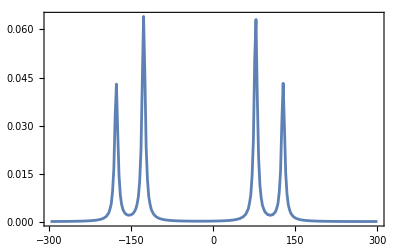

```mathematica
ListPlot[Re@FT@sig]
```

#### ZeroFill and LineBroadening

The processing options ZeroFill and LineBroadening may be used on a time-domain signal in exactly the same way as for a frequency-domain signal (see above).

The option DigitalFrequencyResolution has no effect in the case of a time-domain signal.

## Multiplying and combining signals

### multiplying the Signal by a complex number: phase correction

#### multiplying Signal before FT

A Signal object may be multiplied by a complex number. This is a convenient way to scale up or down the signal, and to perform a phase adjustment.

```mathematica
H=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig=Signal1D[{{2π 600, "1k"}},H]
```

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 860.59×10^-3 rad s^-1.

Signal[{0,1.70333,1.66667×10^-3}, {Lorentzian,<<4>>}]

```mathematica
ListPlot@Re@FT@sig
```

-Graphics-

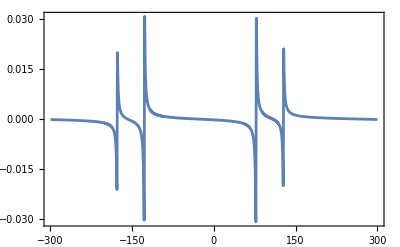

```mathematica
ListPlot@Re@FT@(I*sig)
```

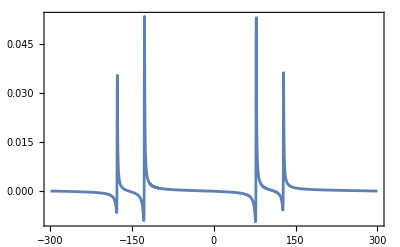

```mathematica
ListPlot@Re@FT@(Exp[I π/4]*sig)
```

#### multiplying Signal after FT

The same manipulation may be done after FT: However in this case, a more complex syntax is needed, since the complex multiplication must only be performed on the signal amplitudes, and not upon the frequency coordinates:

```mathematica
ListPlot@Re@(Map[({1,Exp[I π/4]}*#)&,FT@sig])
```

-Graphics-

This may be used in a simple routine for interactive zero-order phase-correction:

```mathematica
spectrum=FT@sig;
Manipulate[
ListPlot[
Re@(Map[({1,Exp[I ϕ]}*#)&,spectrum]),
PlotRange->{-0.07,0.07}
],
{{ϕ,0,Dynamic[ToString[Round[ϕ/°]]<>"°"]},-π,π,π/180}
]
```

### combining Signal objects

Two or more Signal objects may be combined together using CombineData. The general syntax is:
	CombineData[{sig1,sig2..},{w1,w2..}]
where {w1,w2..} are weighting factors. 
The result is formally sig = sig1*w1 + sig2*w2 +...

If the weights are omitted, uniform weighting is assumed.

In the example below, two simulations are performed, with different spin Hamiltonians:

```mathematica
H1=2π 100 opI[1,"z"]+2π (-150)opI[2,"z"]+2π 50 opI[1].opI[2];
sig1=Signal1D[{{2π 600, "1k"}},H1]
```

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 860.59×10^-3 rad s^-1.

Signal[{0,1.70333,1.66667×10^-3}, {Lorentzian,<<4>>}]

```mathematica
H2=2π 50 opI["z"];
sig2=Signal1D[{{2π 600, "1k"}},H2]
```

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 860.59×10^-3 rad s^-1.

Signal[{0,1.70333,1.66667×10^-3}, {Lorentzian,<<1>>}]

The signals are combined (with equal weights) and plotted as follows:

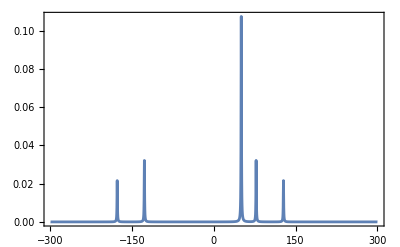

```mathematica
ListPlot@Re@FT@CombineData[{sig1,sig2}]
```

The relative weights may be adjusted as follows:

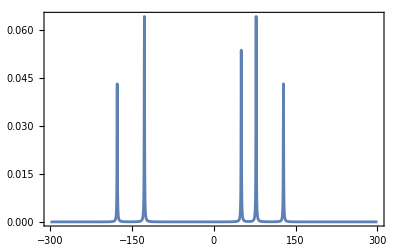

```mathematica
ListPlot@Re@FT@CombineData[{sig1,sig2},{1,1/4}]
```

The weights may also be complex:

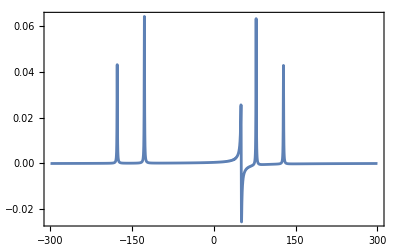

```mathematica
ListPlot@Re@FT@CombineData[{sig1,sig2},{1,-I/4}]
```